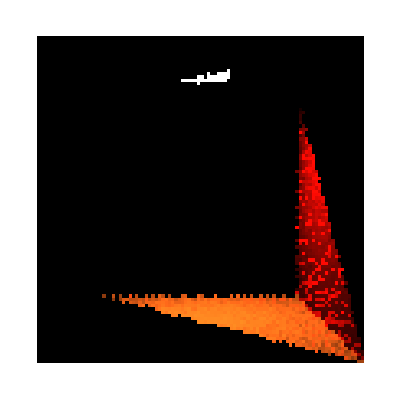

```mathematica
SetDirectory[FileNameJoin@{ParentDirectory[NotebookDirectory[]],"Shared"}];
Needs["gPlots3DEx`"];
Needs["gPlotsEx`"]; 
Needs["gBRDF`"];
Needs["gUtils`"];
Needs["pbrtPath`"];
SetDirectory[NotebookDirectory[]];

ClearAll[rtGetPixelIndex,rtPathL,rtPathPlotScene,rtPathValidatePixel,rtPathValidateScene,testData,debugPixel];

(*CPathExporter::rtGetPixelIndex*)
rtGetPixelIndex[pixel_,resx_]:=Module[
{px,py,index},
px=pixel[[1]];
py=pixel[[2]];

index=px+py*resx;
index
];

(*p863, eq~14.13*)
rtPathL[pixelPath_]:=Module[
{firstLe,bounceIndex,bounceData,beta,li,l},
li={0,0,0};
beta={1,1,1};
For[bounceIndex=0,bounceIndex<3,bounceIndex++,
	bounceData=pixelPath[bounceIndex];
	li+=beta*bounceData["ld"];
	beta*=bounceData["f"]*bounceData["cos"]/bounceData["pdf"];
];

firstLe=pixelPath["le"];
l=firstLe + li;

l
];

rtPathValidatePixel[pixel_,testData_]:=Module[
{keys,pixelIndex,pixelPath,l1,l2},
pixelIndex=rtGetPixelIndex[pixel,testData["resx"]];

keys=Keys[testData];
If[!MemberQ[keys,pixelIndex],Return["no pixel in file"]];

pixelPath=testData[pixelIndex][[1]];

l1=rtPathL[pixelPath];
l2=pixelPath["l"];

{gColorEquals[l1,l2],l1,l2}
];

rtPathValidateScene[testData_]:=Module[
{resx,resy,keys,i,j,pixel,pixelIndex,stats,bok},
resx=testData["resx"];
resy=testData["resy"];
keys=Keys[testData];
stats=<|"total"->0,"fails"->0,"aFail"->""|>;

For[i=0,i<resx,i++,
For[j=0,j<resy,j++,
pixel={i,j};
pixelIndex=rtGetPixelIndex[pixel,resx];
If[!MemberQ[keys,pixelIndex],Continue[]];
stats["total"]+=1;
bok=rtPathValidatePixel[pixel,testData][[1]];
If[!bok,stats["fails"]+=1;stats["aFail"]=pixel;];
];
];

stats
];

rtPathPlotScene[testData_,colorMul_]:=Module[
{keys,resx,resy,imgTable,i,j,pixel,pixelIndex,pixelPath},
resx=testData["resx"];
resy=testData["resy"];
keys=Keys[testData];

imgTable=Table[1,resx,resy];
For[i=1,i<=resx,i++,
		For[j=1,j<=resy,j++,
pixel={j-1,i-1};
pixelIndex=rtGetPixelIndex[pixel,resx];
imgTable[[i]][[j]]=RGBColor[0,0,0];
If[!MemberQ[keys,pixelIndex],Continue[]];
pixelPath=testData[pixelIndex][[1]];
imgTable[[i]][[j]]=RGBColor[pixelPath["l"]*colorMul];
		];
	];

Show[ArrayPlot[imgTable]]
];

debugPixel={58,10};
testData=ToExpression[Import["cornell-tiny.path"]];
(*rtPathValidatePixel[debugPixel,testData]*)
(*rtPathValidateScene[testData]*)
rtPathPlotScene[testData,10]
```